#### gr. 1

Zad. 1

```mathematica
Together[1/(x+3)+3/(x-2)];
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(7+4 x)/(-6+x+x^2)

3 Log[2-x]+Log[3+x]

Zad. 2

{{x→0},{x→3}}

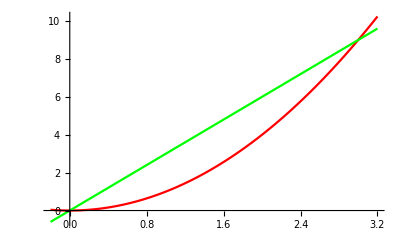

9/2

```mathematica
y1=x^2;
y2=3x;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-0.2,3.2},PlotStyle->{Red,Green}]
Integrate[y2-y1,{x,0,3}]
```

Zad. 3

```mathematica
z=x^2-2 x y +y^3;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

2 x-2 y

-2 x+3 y^2

{{x→0,y→0},{x→2/3,y→2/3}}

{-4,4}

{2,2}

#### gr. 2

Zad. 1

```mathematica
Together[3/(x+3)-7/(x+3)^2]
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(2+3 x)/(3+x)^2

(2+3 x)/(9+6 x+x^2)

7/(3+x)+3 Log[3+x]

Zad. 2

```mathematica
π Integrate[(2-x)^2,{x,1,2}]
```

π/3

Zad. 3

```mathematica
z=-x^3+3x y-y^2- y;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-3 x^2+3 y

-1+3 x-2 y

{{x→1/2,y→1/4},{x→1,y→1}}

{-3,3}

{-3,-6}